## Gaussian Orthogonal Ensemble

### Matrix size and matrix elements variance

```mathematica
n=3000;
sigma2=1;
```

### Random matrix and its spectrum

```mathematica
a=RandomVariate[NormalDistribution[0,sigma2],{n,n}];
GOEMatrix=(a+Transpose[a])/2;
```

```mathematica
energies=Sort[Eigenvalues[GOEMatrix]];
```

### Histogram and Wigner semicircle law

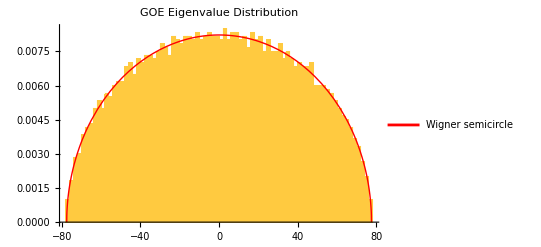

```mathematica
hist=Histogram[energies,100,"PDF",PlotRange->All,FrameLabel->{"Eigenvalue","Density"},PlotLabel->"GOE Eigenvalue Distribution"];
wignerSemicircle[e_]:=(1/(π sigma2 n)) Sqrt[2sigma2 n-e^2]
semicirclePlot=Plot[wignerSemicircle[x],{x,-sigma2 √(2n),sigma2 √(2n)},PlotStyle->{Thick,Red},PlotLegends->{"Wigner semicircle"},PlotRange->All];
Show[hist,semicirclePlot]
```

### Unfolding

#### ...using the Wigner semicircle law

```mathematica
integratedSemicircle[e_]:=1/2+n Integrate[wignerSemicircle[x],x]/.x->e
```

```mathematica
unfolded=Re[integratedSemicircle[energies]];
```

Unfolded Level density :

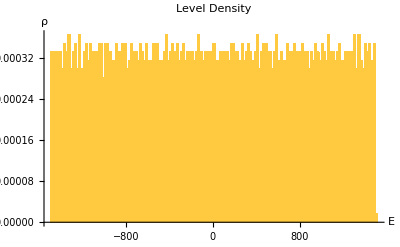

```mathematica
Histogram[unfolded,100,"PDF",PlotLabel->"Level Density",AxesLabel->{"E","ρ"}]
```

Level spacing and histogram

```mathematica
spacings=Differences[unfolded];
```

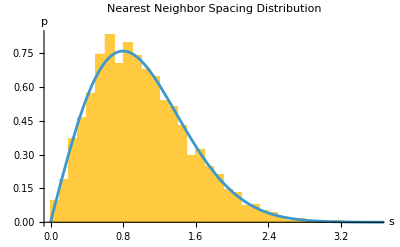

```mathematica
Show[{Histogram[spacings,{0.1},"PDF",PlotLabel->"Nearest Neighbor Spacing Distribution",AxesLabel->{"s","p"}],Plot[π/2 s Exp[-π/4 s^2],{s,0,5},PlotLegends->"Wigner-Dyson distribution"]}]
```

#### Polynomial unfolding

```mathematica
cumulLDdata=Transpose[{energies,Table[j,{j,1,n}]}];
```

Degree of the polynomial :

```mathematica
d=10;
```

```mathematica
fit=Fit[cumulLDdata,Table[x^k,{k,0,d}],x]
```

1500.84+24.656 x-0.00141518 x^2-0.000640887 x^3+1.50971×10^-6 x^4-5.92875×10^-8 x^5-7.16032×10^-10 x^6+1.18852×10^-11 x^7+1.44363×10^-13 x^8-1.43636×10^-15 x^9-1.01951×10^-17 x^10

```mathematica
unfolded=fit/.x->energies;
```

Unfolded Level density :

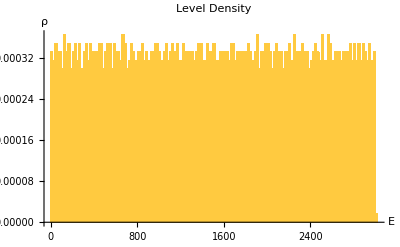

```mathematica
Histogram[unfolded,100,"PDF",PlotLabel->"Level Density",AxesLabel->{"E","ρ"}]
```

Level spacing and histogram

```mathematica
spacings=Differences[unfolded];
```

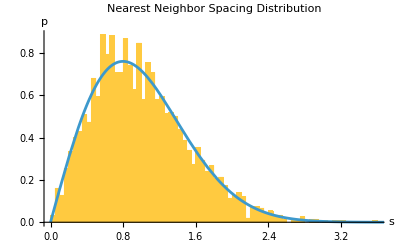

```mathematica
Show[{Histogram[spacings,100,"PDF",PlotLabel->"Nearest Neighbor Spacing Distribution",AxesLabel->{"s","p"}],Plot[π/2 s Exp[-π/4 s^2],{s,0,5},PlotLegends->"Wigner-Dyson distribution"]}]
```

### Ratios of consecutive spacings

```mathematica
spacings=Differences[energies];
ratios=spacings[[2;;-1]]/spacings[[1;;-2]];
ratiost=If[#>1,1/#,#]&/@ratios;
```

Mean value:

```mathematica
Mean[ratiost]
```

0.54023

Theoretically it should be

```mathematica
4-2 √3//N
```

0.535898

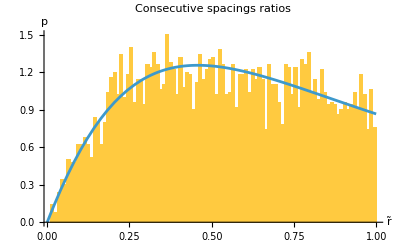

```mathematica
Show[{Histogram[ratiost,100,"PDF",PlotLabel->"Consecutive spacings ratios",AxesLabel->{"r̃","p"}],Plot[27/4(r+r^2)/((1+r+r^2)^(5/2)),{r,0,1}]}]
```

## Ensemble of Random matrices